```mathematica
SetDirectory[NotebookDirectory[]]
```

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]]
];

result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDSpace = 1;
IDRho = 1+IDSpace;
IDvx = 2+IDSpace;
IDtheta = 3+IDSpace;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = √2;
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;

trialsol
]
```

## Poisson Heat conduction

### G20

```mathematica
ndof=384;
foldername = "Tests/build/output_N6_poisson_heat_conduction_1D_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
exactsol20 = importdata[ndof,1,"_global_",1,foldername];
numsol20 = ConvToPrim[numsol20];
exactsol20 = ConvToPrim[exactsol20];
```

#### θ

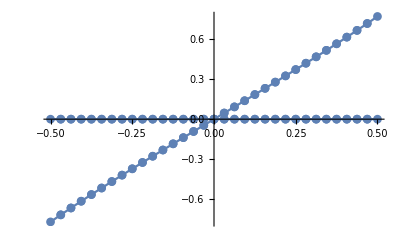

```mathematica
plot1=Show[ListPlot[numsol20⟦All,{1,IDtheta}⟧,Joined->True,PlotMarkers->Automatic],ListPlot[exactsol20⟦All,{1,IDtheta}⟧,Joined->True,PlotMarkers->Automatic]]
```

### G26

```mathematica
ndof=16384;
foldername = "Tests/build/output_G26_odd_poisson_1D_Kn0p1";
numsol26=importdata[ndof,1,"_global_",0,foldername];
numsol26 = ConvToPrim[numsol26];
```

#### θ

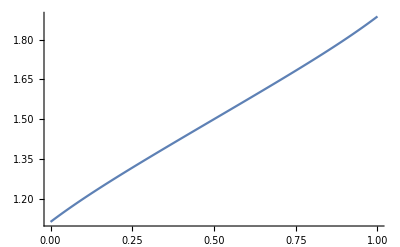

```mathematica
ListPlot[numsol26⟦All,{1,IDtheta}⟧,Joined->True]
```